Solve for the EPs

```mathematica
S=Solve[-x^3+d x+c==0,x]//FullSimplify
```

{{x→-(2 3^(1/3) d+2^(1/3) (-9 c+√(81 c^2-12 d^3))^(2/3))/(6^(2/3) (-9 c+√(81 c^2-12 d^3))^(1/3))},{x→((-1)^(1/3) (2 3^(1/3) d-(-2)^(1/3) (-9 c+√(81 c^2-12 d^3))^(2/3)))/(6^(2/3) (-9 c+√(81 c^2-12 d^3))^(1/3))},{x→(-2 (-3)^(2/3) d+(-6)^(1/3) (-9 c+√(81 c^2-12 d^3))^(2/3))/(3 2^(2/3) (-9 c+√(81 c^2-12 d^3))^(1/3))}}

Plot the 3 branches to discover that it is the third (green) one we want

```mathematica
Plot3D[{x/.S[[1]],x/.S[[2]],x/.S[[3]]},{c,-4,4},{d,0,4}]
```

-Graphics3D-

Plot that branch with higher resolution

```mathematica
Plot3D[Evaluate[x/.S[[3]]],{c,-4,4},{d,0,4},MaxRecursion->7,WorkingPrecision->24]
```

-Graphics3D-

Plot slices for different d values to see the cross-sectional shape of this branch

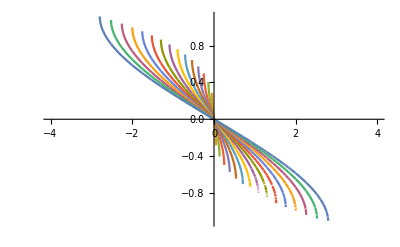

```mathematica
Plot[Evaluate[Table[Evaluate[x/.S[[3]]],{d,1/100000,4,1/4}]],{c,-4,4},PlotPoints->300]
```

Approximation for normal distribution CDF

```mathematica
approx[z_] := 1/(1+Exp[-1.5976*z-0.07056(z^3)])
transformApprox[z_,mu_,sigma_]:=approx[(z+mu)/Sqrt[sigma]]
```

Find the X such that normal CDF (mean=0,std=1) is 70%

```mathematica
Z = Solve[approx[z]==0.7,z]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{z→-0.262001-4.77992 ⅈ},{z→-0.262001+4.77992 ⅈ},{z→0.524002}}

```mathematica
Cs = Re[Solve[(x/.S⟦3⟧)==(z/.Z[[3]]),{c,d}]//Simplify]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Re[c→0.14388-0.524002 d-(8.02489×10^-17+2.94609×10^-17 ⅈ) d^(3/2)]},{Re[c→0.14388-0.524002 d+(8.02489×10^-17+2.94609×10^-17 ⅈ) d^(3/2)]}}

```mathematica
Plot3D[{Evaluate[x/.S[[3]]],c==0.14387953597946684-0.5240020783227919 d},{c,-4,4},{d,0,4},MaxRecursion->8,WorkingPrecision->24]
```

Plot3D::precw: The precision of the argument function (c==0.14388-0.524002 d) is less than WorkingPrecision (24.).

-Graphics3D-

```mathematica
x/.S[[3]]
```

(-2 (-3)^(2/3) d+(-6)^(1/3) (-9 c+√(81 c^2-12 d^3))^(2/3))/(3 2^(2/3) (-9 c+√(81 c^2-12 d^3))^(1/3))

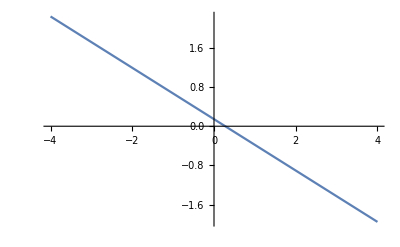

```mathematica
Plot[0.14387953597946684-0.5240020783227919 d,{d,-4,4}]
```

```mathematica
Plot[,{c,-4,4},PlotPoints->300]
```

```mathematica
Solve[c==0.14387953597946684-0.5240020783227919 d,d]//FullSimplify
```

{{d→0.274578-1.90839 c}}